```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yuichirotada/Documents/Univ/DESI/math

## formulae

```mathematica
V[x_]=Vi+Vp x+1/2 Vpp x^2;
```

```mathematica
u[t_]=x[t] a[t]^(3/2);
```

```mathematica
u''[t]+(Vpp-3/4 Vi)u[t]+Vp a[t]^(3/2)/.{a'[t]->a[t]H[t],a''[t]->D[(a[t]H[t]), t],x''[t]->-3H[t]x'[t]-V'[x[t]]}/.{a'[t]->a[t]H[t],H'[t]->-1/2(ρm+ρϕ+pϕ)}/.{H[t]^2->1/3(ρm+ρϕ)}//Simplify
```

-3/4 (pϕ+Vi) a[t]^(3/2) x[t]

```mathematica
uu[t_]=A Sinh[k t]+B Cosh[k t]+Sqrt[(1-Ωϕ)/Ωϕ](Vp tΛ^2)/(k^2 tΛ^2-1)Sinh[t/tΛ]/.{k->Sqrt[3/4 Vi-Vpp],tΛ->2/Sqrt[3Vi]}//Simplify
```

B Cosh[t √((3 Vi)/4-Vpp)]-(Vp √(-1+1/Ωϕ) Sinh[1/2 √3 t √Vi])/Vpp+A Sinh[t √((3 Vi)/4-Vpp)]

```mathematica
Simplify[uu''[t]+(Vpp-3/4 Vi)uu[t]+Vp(((1-Ωϕ)/Ωϕ)^(1/3)Sinh[t/tΛ]^(2/3))^(3/2)/.{tΛ->2/Sqrt[3Vi]},Sinh[1/2 Sqrt[3]t Sqrt[Vi]]>0]
```

0

```mathematica
aa[t_]=((1-Ωϕ)/Ωϕ)^(1/3)Sinh[t/tΛ]^(2/3)/.{tΛ->2/Sqrt[3 3 H0^2 Ωϕ]}
```

((1-Ωϕ)/Ωϕ)^(1/3) Sinh[3/2 t √(H0^2 Ωϕ)]^(2/3)

```mathematica
Simplify[(aa'[t]/aa[t])^2,H0>0]
Simplify[H0^2((1-Ωϕ)aa[t]^-3+Ωϕ),H0>0]
```

H0^2 Ωϕ Coth[3/2 H0 t √Ωϕ]^2

H0^2 Ωϕ Coth[3/2 H0 t √Ωϕ]^2

```mathematica
xx[t_]=Vp/Vpp(Sinh[k t]/(k tΛ Sinh[t/tΛ])-1)/.{k->Sqrt[3/4 Vi-Vpp],tΛ->2/Sqrt[3Vi]}
```

(Vp (-1+(√3 √Vi Csch[1/2 √3 t √Vi] Sinh[t √((3 Vi)/4-Vpp)])/(2 √((3 Vi)/4-Vpp))))/Vpp

```mathematica
Normal[Series[xx[t],{t,0,0}]]
Normal[Series[xx'[t],{t,0,0}]]
```

0

0

```mathematica
aa[t_]=((1-Ωϕ)/Ωϕ)^(1/3)Sinh[t/tΛ]^(2/3)/.{tΛ->2/Sqrt[3 Vi]}
un[t_]=xx[t] aa[t]^(3/2)//Simplify
```

((1-Ωϕ)/Ωϕ)^(1/3) Sinh[1/2 √3 t √Vi]^(2/3)

(Vp ((-1+1/Ωϕ)^(1/3) Sinh[1/2 √3 t √Vi]^(2/3))^(3/2) (-1+(√3 √Vi Csch[1/2 √3 t √Vi] Sinh[t √((3 Vi)/4-Vpp)])/(√(3 Vi-4 Vpp))))/Vpp

```mathematica
Simplify[un''[t]+(Vpp-3/4 Vi)un[t]+Vp(((1-Ωϕ)/Ωϕ)^(1/3)Sinh[t/tΛ]^(2/3))^(3/2)/.{tΛ->2/Sqrt[3Vi]},Sinh[1/2 Sqrt[3]t Sqrt[Vi]]>0]
```

0

```mathematica
xx[t_]=Vp/Vpp(Sinh[k t]/(k tΛ Sinh[t/tΛ])-1);
wp1[t_]=3/4(Vp/(k tΛ Vpp))^2((k tΛ Cosh[k t]Sinh[t/tΛ]-Sinh[k t]Cosh[t/tΛ])/Sinh[t/tΛ]^2)^2;
xx'[t]^2/Vi-wp1[t]/.{Vi->4/(3 tΛ^2)}//Simplify
```

0

```mathematica
aa[t_]=((1-Ωϕ)/Ωϕ)^(1/3)Sinh[t/tΛ]^(2/3);
tt[a_]=Simplify[InverseFunction[aa][a],{-1+1/Ωϕ>0}]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

tΛ ArcSinh[a^(3/2)/(√(-1+1/Ωϕ))]

```mathematica
Ft[a_]=Sqrt[Ωϕ+(1-Ωϕ)a^-3];
wp1n[a_]=Simplify[a^(3(K-1))(((Ωϕ^(1/2)K-Ft[a])(Ft[a]+Ωϕ^(1/2))^K+(Ωϕ^(1/2)K+Ft[a])(Ft[a]-Ωϕ^(1/2))^K)/((Ωϕ^(1/2)K-1)(1+Ωϕ^(1/2))^K+(Ωϕ^(1/2)K+1)(1-Ωϕ^(1/2))^K))^2,{Ωϕ>0,K>0}]
```

(a^(3 (-1+K)) ((K √Ωϕ-√((1-Ωϕ)/a^3+Ωϕ)) (√Ωϕ+√((1-Ωϕ)/a^3+Ωϕ))^K+(-√Ωϕ+√((1-Ωϕ)/a^3+Ωϕ))^K (K √Ωϕ+√((1-Ωϕ)/a^3+Ωϕ)))^2)/(((1+√Ωϕ)^K (-1+K √Ωϕ)+(1-√Ωϕ)^K (1+K √Ωϕ))^2)

```mathematica
w0p1=wp1[tt[1]]//TrigToExp//Simplify
```

-(3 Vp^2 (1/(√(-1+1/Ωϕ))+√(1/(1-Ωϕ)))^(-2 k tΛ) (k tΛ (1+(1/(√(-1+1/Ωϕ))+√(1/(1-Ωϕ)))^(2 k tΛ))-(-1+(1/(√(-1+1/Ωϕ))+√(1/(1-Ωϕ)))^(2 k tΛ)) √(-1+1/Ωϕ) √(1/(1-Ωϕ)))^2 (-1+Ωϕ))/(16 k^2 tΛ^2 Vpp^2 Ωϕ)

```mathematica
Simplify[wp1[t]/(w0p1 wp1n[aa[t]])/.{K->k tΛ}//TrigToExp,{k>0,tΛ>0,-1+1/Ωϕ>0,t>0,Ωϕ>0,1-Ωϕ>0}]
```

((1-√Ωϕ)^(-2 k tΛ) ((1-√Ωϕ)^(k tΛ)-(1+√Ωϕ)^(k tΛ)+k tΛ ((1-√Ωϕ)^(k tΛ)+(1+√Ωϕ)^(k tΛ)) √Ωϕ)^2)/((1-((1+√Ωϕ)/(√(1-Ωϕ)))^(2 k tΛ)+k tΛ (1+((1+√Ωϕ)/(√(1-Ωϕ)))^(2 k tΛ)) √Ωϕ)^2)

```mathematica
Simplify[(1-Sqrt[Ωϕ])^(k tΛ)(1-((1+√Ωϕ)/(√(1-Ωϕ)))^(2 k tΛ)+k tΛ (1+((1+√Ωϕ)/(√(1-Ωϕ)))^(2 k tΛ)) √Ωϕ)-((1-√Ωϕ)^(k tΛ)-(1+√Ωϕ)^(k tΛ)+k tΛ ((1-√Ωϕ)^(k tΛ)+(1+√Ωϕ)^(k tΛ)) √Ωϕ),{1-Ωϕ>0,k>0,tΛ>0}]
```

0

```mathematica
3((1+Ωϕinv^(1/2))^K(-1+Ωϕinv+(K-Ωϕinv^(1/2))^2)-(-1+Ωϕinv^(1/2))^K(-1+Ωϕinv+(K+Ωϕinv^(1/2))^2))/(((K-Ωϕinv^(1/2))(1+Ωϕinv^(1/2))^K+(K+Ωϕinv^(1/2))(-1+Ωϕinv^(1/2))^K)Ωϕinv^(1/2))
```

(3 ((1+√Ωϕinv)^K (-1+(K-√Ωϕinv)^2+Ωϕinv)-(-1+√Ωϕinv)^K (-1+(K+√Ωϕinv)^2+Ωϕinv)))/(((K-√Ωϕinv) (1+√Ωϕinv)^K+(-1+√Ωϕinv)^K (K+√Ωϕinv)) √Ωϕinv)

```mathematica
FullSimplify[wp1n'[1]-3((1+Ωϕinv^(1/2))^K(-1+Ωϕinv+(K-Ωϕinv^(1/2))^2)-(-1+Ωϕinv^(1/2))^K(-1+Ωϕinv+(K+Ωϕinv^(1/2))^2))/(((K-Ωϕinv^(1/2))(1+Ωϕinv^(1/2))^K+(K+Ωϕinv^(1/2))(-1+Ωϕinv^(1/2))^K)Ωϕinv^(1/2))/.{Ωϕ->Ωϕinv^-1},{Ωϕinv>0}]
```

0

```mathematica
Normal[Series[Vp/Vpp(Sinh[k t]/(k tΛ Sinh[t/tΛ])-1),{t,0,2}]]/.{k^2->3/4 Vi-Vpp,tΛ^2->4/(3Vi)}//Simplify
```

-(2 t^2 Vp)/(9 tΛ^2 Vi)

```mathematica
G[a_]=Simplify[(K Sqrt[(a^3 Ωϕ)/(1-Ωϕ)]Cosh[K ArcSinh[Sqrt[(a^3 Ωϕ)/(1-Ωϕ)]]]-Sqrt[1+(a^3 Ωϕ)/(1-Ωϕ)]Sinh[K ArcSinh[Sqrt[(a^3 Ωϕ)/(1-Ωϕ)]]])/((a^3 Ωϕ)/(1-Ωϕ))//TrigToExp,{Ωϕ>0,1-Ωϕ>0,a>0,K>0}]
```

((-1+Ωϕ) (√(-(a^3 Ωϕ)/(-1+Ωϕ))+√((-1+Ωϕ-a^3 Ωϕ)/(-1+Ωϕ)))^-K (√((-1+Ωϕ-a^3 Ωϕ)/(-1+Ωϕ)) (-1+(√(-(a^3 Ωϕ)/(-1+Ωϕ))+√((-1+Ωϕ-a^3 Ωϕ)/(-1+Ωϕ)))^(2 K))-K √(-(a^3 Ωϕ)/(-1+Ωϕ)) (1+(√(-(a^3 Ωϕ)/(-1+Ωϕ))+√((-1+Ωϕ-a^3 Ωϕ)/(-1+Ωϕ)))^(2 K))))/(2 a^3 Ωϕ)

```mathematica
G1=FullSimplify[G[1],{Ωϕ>0,1-Ωϕ>0,K>0}]
```

(((1+√Ωϕ)^(2 K) (-1+K √Ωϕ)+(1+K √Ωϕ) (1-Ωϕ)^K) (1+√Ωϕ)^-K (1-Ωϕ)^(1/2-K/2))/(2 Ωϕ)

```mathematica
Vn[a_]=1-1/2(1+w0)(K^2(1-K^2))/G1^2(1-((1-Ωϕ)Sinh[K ArcSinh[Sqrt[(a^3 Ωϕ)/(1-Ωϕ)]]]^2)/(a^3 K^2 Ωϕ))//TrigToExp//Simplify;
Kn[a_]=(1+w0)/2 G[a]^2/G1^2;
ρt[a_]=Vn[a]+Kn[a];
```

```mathematica
FullSimplify[Ωϕ/ρt[1],{Ωϕ>0,1-Ωϕ>0,K>0}]
```

(2 ((1+√Ωϕ)^(2 K) (-1+K √Ωϕ)+(1+K √Ωϕ) (1-Ωϕ)^K)^2 Ωϕ)/((1+√Ωϕ)^(4 K) (3+w0-2 K (3+w0) √Ωϕ+(1+2 K^2+w0) Ωϕ)+(1-Ωϕ)^(2 K) (3+w0+2 K (3+w0) √Ωϕ+(1+2 K^2+w0) Ωϕ)+2 (1+√Ωϕ)^(2 K) (1-Ωϕ)^(-1+K) (-3-w0+2 (1+K^2 (2+w0)) Ωϕ+(1+w0+2 K^4 (1+w0)-2 K^2 (3+2 w0)) Ωϕ^2))

```mathematica
wp1pheno[tt_]=Simplify[wp1[tt/Sqrt[Vi]]/.{k->Sqrt[3/4 Vi-Vpp],tΛ->Sqrt[4/(3Vi)]}/.{Vpp->3/4(1-K^2)Vi,Vp->-Sqrt[3/4(1+w0)K^2((1-K^2)^2)/G[1]^2]Vi},{K>0,Vi>0}]
```

(4 (1+w0) Ωϕ^2 (√(1/(1-Ωϕ))+√(-Ωϕ/(-1+Ωϕ)))^(2 K) Csch[(√3 tt)/2]^2 (K Cosh[1/2 √3 K tt]-Coth[(√3 tt)/2] Sinh[1/2 √3 K tt])^2)/((-1+Ωϕ)^2 (√(1/(1-Ωϕ)) (-1+(√(1/(1-Ωϕ))+√(-Ωϕ/(-1+Ωϕ)))^(2 K))-K √(-Ωϕ/(-1+Ωϕ)) (1+(√(1/(1-Ωϕ))+√(-Ωϕ/(-1+Ωϕ)))^(2 K)))^2)

```mathematica
wp1phenoa[a_]=Simplify[wp1pheno[Sqrt[Vi]tt[a]]/.{tΛ->Sqrt[4/(3Vi)]}//TrigToExp,{Vi>0}]
```

(4 (1+w0) Ωϕ^2 (√(1/(1-Ωϕ))+√(-Ωϕ/(-1+Ωϕ)))^(2 K) (a^(3/2)/(√(-1+1/Ωϕ))+√((-1+Ωϕ-a^3 Ωϕ)/(-1+Ωϕ)))^(2-2 K) (-1+K-(a^(3/2)/(√(-1+1/Ωϕ))+√((-1+Ωϕ-a^3 Ωϕ)/(-1+Ωϕ)))^2-K (a^(3/2)/(√(-1+1/Ωϕ))+√((-1+Ωϕ-a^3 Ωϕ)/(-1+Ωϕ)))^2+(a^(3/2)/(√(-1+1/Ωϕ))+√((-1+Ωϕ-a^3 Ωϕ)/(-1+Ωϕ)))^(2 K)+K (a^(3/2)/(√(-1+1/Ωϕ))+√((-1+Ωϕ-a^3 Ωϕ)/(-1+Ωϕ)))^(2 K)+(a^(3/2)/(√(-1+1/Ωϕ))+√((-1+Ωϕ-a^3 Ωϕ)/(-1+Ωϕ)))^(2 (1+K))-K (a^(3/2)/(√(-1+1/Ωϕ))+√((-1+Ωϕ-a^3 Ωϕ)/(-1+Ωϕ)))^(2 (1+K)))^2)/((-1+Ωϕ)^2 (-1+(a^(3/2)/(√(-1+1/Ωϕ))+√((-1+Ωϕ-a^3 Ωϕ)/(-1+Ωϕ)))^2)^4 (√(1/(1-Ωϕ)) (-1+(√(1/(1-Ωϕ))+√(-Ωϕ/(-1+Ωϕ)))^(2 K))-K √(-Ωϕ/(-1+Ωϕ)) (1+(√(1/(1-Ωϕ))+√(-Ωϕ/(-1+Ωϕ)))^(2 K)))^2)

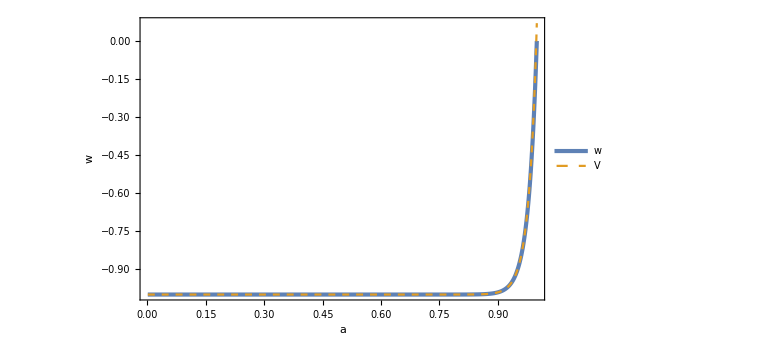

```mathematica
Plot[{wp1phenoa[a]-1/.{w0->0,K->20,Ωϕ->1-0.325},(Kn[a]-Vn[a])/ρt[a]/.{w0->0,K->20,Ωϕ->1-0.325}},{a,10^-3,1},PlotRange->Full,PlotStyle->{AbsoluteThickness[3],Dashed},FrameLabel->{{w,None},{a,Row[{Subscript[w, 0]==0,",  ",K==20}]}},PlotLegends->Placed[{w,V},{0.2,0.7}]]
```

```mathematica
ρtw[a_]:=Exp[-3NIntegrate[wp1phenoa[ap]/.{w0->0,K->20,Ωϕ->1-0.325},{ap,1,a}]]
```

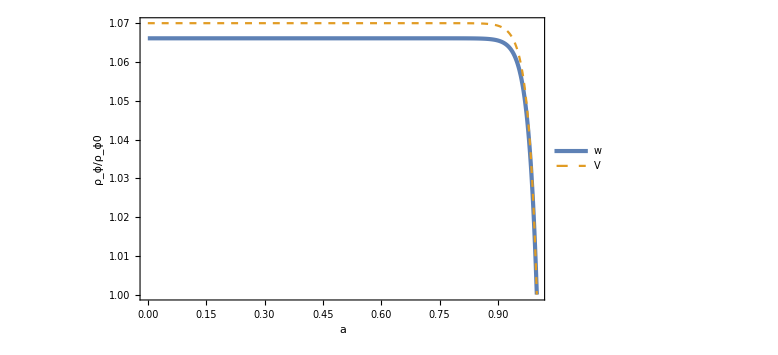

```mathematica
Plot[{ρtw[a],ρt[a]/ρt[1]/.{w0->0,K->20,Ωϕ->1-0.325}},{a,0,1},PlotRange->Full,PlotStyle->{AbsoluteThickness[3],Dashed},FrameLabel->{{Row[{Subscript[ρ, ϕ],"/",Subscript[ρ, ϕ0]}],None},{a,Row[{Subscript[w, 0]==0,",  ",K==20}]}},PlotLegends->Placed[{w,V},{0.2,0.2}]]
```

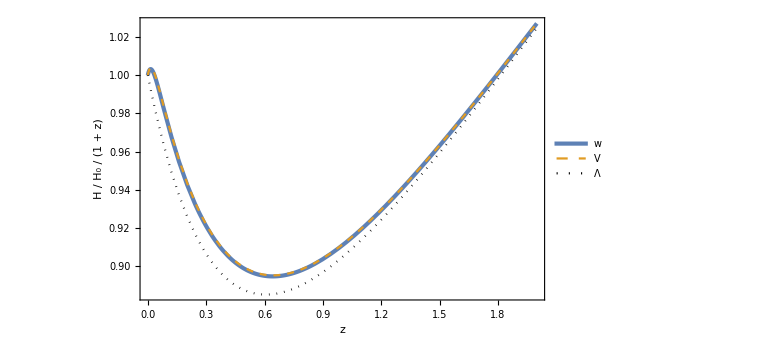

```mathematica
Plot[{Sqrt[(1-Ωϕ)(1+z)^3+Ωϕ ρtw[1/(1+z)]]/(1+z)/.{Ωϕ->1-0.325},Sqrt[(1-Ωϕ)(1+z)^3+Ωϕ ρt[1/(1+z)]/ρt[1]]/(1+z)/.{w0->0,K->20,Ωϕ->1-0.325},
Sqrt[(1-Ωϕ)(1+z)^3+Ωϕ]/(1+z)/.{Ωϕ->1-0.325}},{z,0,2},PlotRange->Full,PlotStyle->{AbsoluteThickness[3],Dashed,{Black,Dotted}},FrameLabel->{{Row[{H," / ",Subscript[H, 0]," / (1 + z)"}],None},{z,Row[{Subscript[w, 0]==0,",  ",K==20}]}},PlotLegends->Placed[{w,V,Λ},{0.4,0.75}]]
```

## Hayashi

```mathematica
Union1s=Import["HayashiUni1s.csv"];
Union2s=Import["HayashiUni2s.csv"];
Union2sLeft=Select[Union2s,#[[1]]<-0.75&];
Union2sRight=Select[Union2s,#[[1]]>-0.75&];
```

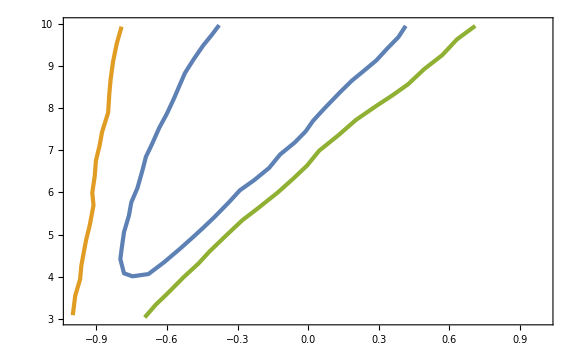

```mathematica
ListPlot[{Union1s,Union2sLeft,Union2sRight},PlotRange->{{-1,1},{3,10}}]
```

```mathematica
F[a_]=Sqrt[1+(Ωϕ^-1-1)a^-3];
calF[a_]=(((KK-F[a])(F[a]+1)^KK+(KK+F[a])(F[a]-1)^KK)/((KK-Ωϕ^(-1/2))(Ωϕ^(-1/2)+1)^KK+(KK+Ωϕ^(-1/2))(Ωϕ^(-1/2)-1)^KK))^2;
w[a_]=-1+(1+w0)a^(3(KK-1))calF[a];
```

```mathematica
wmax2s[z_]:=Max[Join[Table[w[1/(1+z)]/.{w0->Union2s[[i,1]],KK->Union2s[[i,2]],Ωϕ->1-0.325},{i,Length[Union2s]}],Table[w[1/(1+z)]/.{KK->3,Ωϕ->1-0.325},{w0,-1,-0.7,0.01}],Table[w[1/(1+z)]/.{KK->10,Ωϕ->1-0.325},{w0,-0.8,0.7,0.01}]]]
wmin2s[z_]:=Min[Join[Table[w[1/(1+z)]/.{w0->Union2s[[i,1]],KK->Union2s[[i,2]],Ωϕ->1-0.325},{i,Length[Union2s]}],Table[w[1/(1+z)]/.{KK->3,Ωϕ->1-0.325},{w0,-1,-0.7,0.01}],Table[w[1/(1+z)]/.{KK->10,Ωϕ->1-0.325},{w0,-0.8,0.7,0.01}]]]
wmax1s[z_]:=Max[Join[Table[w[1/(1+z)]/.{w0->Union1s[[i,1]],KK->Union1s[[i,2]],Ωϕ->1-0.325},{i,Length[Union1s]}],Table[w[1/(1+z)]/.{KK->10,Ωϕ->1-0.325},{w0,-0.37,0.4,0.01}]]]
wmin1s[z_]:=Min[Join[Table[w[1/(1+z)]/.{w0->Union1s[[i,1]],KK->Union1s[[i,2]],Ωϕ->1-0.325},{i,Length[Union1s]}],Table[w[1/(1+z)]/.{KK->10,Ωϕ->1-0.325},{w0,-0.37,0.4,0.01}]]]
```

```mathematica
AbsoluteTiming[wmax2sList=Table[{z,wmax2s[z]},{z,0,1,0.01}];
wmin2sList=Table[{z,wmin2s[z]},{z,0,1,0.01}];
wmax1sList=Table[{z,wmax1s[z]},{z,0,1,0.01}];
wmin1sList=Table[{z,wmin1s[z]},{z,0,1,0.01}];]
```

{3.99904,Null}

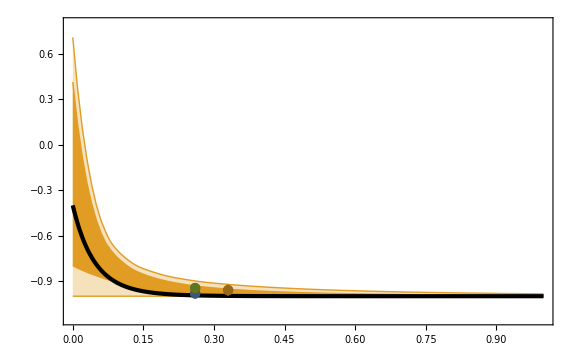

```mathematica
Show[ListPlot[{wmax2sList,wmin2sList},PlotRange->{{0,1},{-1.15,0.8}},PlotStyle->{{Thin,Color[2]}},Filling->{1->{2}},FillingStyle->Directive[Opacity[0.3]]],ListPlot[{wmax1sList,wmin1sList},PlotRange->{{0,1},{-1.15,0.8}},PlotStyle->{{Thin,Color[2]}},Filling->{1->{2}},FillingStyle->Directive[Opacity[1]]],
Plot[w[1/(1+z)]/.{w0->-0.4,KK->10,Ωϕ->1-0.325},{z,0,1},PlotRange->Full,PlotStyle->{Black,AbsoluteThickness[3]}],
ListPlot[{{{0.26,-0.982±0.028}},{{0.33,-0.96±0.038}},{{0.26,-0.946±0.026}}},Joined->False,PlotStyle->{Darker[Color[1]],Darker[Color[2]],Darker[Color[3]]}]]
```

```mathematica
w2sList=Join[Table[{z,w[1/(1+z)]/.{w0->Union2s[[i,1]],KK->Union2s[[i,2]],Ωϕ->1-0.325}},{i,Length[Union2s]},{z,0,1,0.01}],
Table[{z,w[1/(1+z)]/.{KK->3,Ωϕ->1-0.325}},{w0,-1,-0.7,0.02},{z,0,1,0.01}],Table[{z,w[1/(1+z)]/.{KK->10,Ωϕ->1-0.325}},{w0,-0.8,0.7,0.05},{z,0,1,0.01}]];
w1sList=Join[Table[{z,w[1/(1+z)]/.{w0->Union1s[[i,1]],KK->Union1s[[i,2]],Ωϕ->1-0.325}},{i,Length[Union1s]},{z,0,1,0.01}],
Table[{z,w[1/(1+z)]/.{KK->10,Ωϕ->1-0.325}},{w0,-0.37,0.4,0.01},{z,0,1,0.01}]];
```

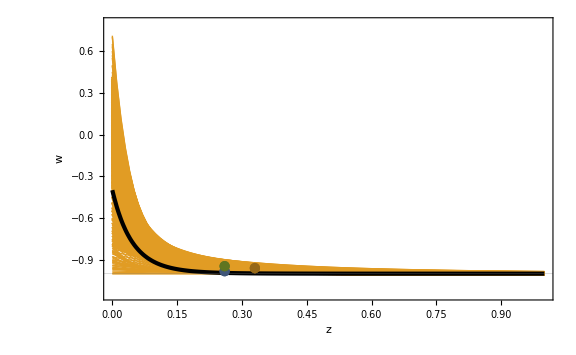

```mathematica
Show[ListPlot[w2sList,PlotRange->{{0,1},{-1.15,0.8}},PlotStyle->{{Thin,Color[2]}},GridLines->{None,{-1}},FrameLabel->{z,w}],ListPlot[w1sList,PlotStyle->{{AbsoluteThickness[2],Color[2]}},PlotRange->Full],Plot[w[1/(1+z)]/.{w0->-0.4,KK->10,Ωϕ->1-0.325},{z,0,1},PlotRange->Full,PlotStyle->{Black,AbsoluteThickness[3]}],
ListPlot[{{{0.26,-0.982±0.028}},{{0.33,-0.96±0.038}},{{0.26,-0.946±0.026}}},Joined->False,PlotStyle->{Darker[Color[1]],Darker[Color[2]],Darker[Color[3]]}]]
```

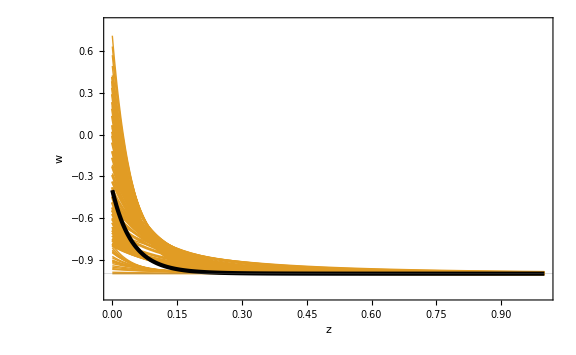

```mathematica
Show[Plot[Table[w[1/(1+z)]/.{w0->Union2s[[i,1]],KK->Union2s[[i,2]],Ωϕ->1-0.325},{i,Length[Union2s]}],{z,0,1},PlotRange->{{0,1},{-1.15,0.8}},PlotStyle->{Thin,Color[2]},GridLines->{None,{-1}},FrameLabel->{z,w}],
Plot[Table[w[1/(1+z)]/.{w0->Union1s[[i,1]],KK->Union1s[[i,2]],Ωϕ->1-0.325},{i,Length[Union1s]}],{z,0,1},PlotStyle->{AbsoluteThickness[2],Color[2]},PlotRange->Full],
Plot[w[1/(1+z)]/.{w0->-0.4,KK->10,Ωϕ->1-0.325},{z,0,1},PlotRange->Full,PlotStyle->{Black,AbsoluteThickness[3]}]]
```

```mathematica
V[x_]=Λ2 f^2(1+Cos[x/f]);
```

```mathematica
ws=-0.707;
Ks=5.42;
Ωms=0.325;
```

```mathematica
G[a_]=(K Sqrt[(a^3 Ωϕ)/(1-Ωϕ)]Cosh[K ArcSinh[Sqrt[(a^3 Ωϕ)/(1-Ωϕ)]]]-Sqrt[1+(a^3 Ωϕ)/(1-Ωϕ)]Sinh[K ArcSinh[Sqrt[(a^3 Ωϕ)/(1-Ωϕ)]]])/((a^3 Ωϕ)/(1-Ωϕ));
Vnorm[a_]=1-1/2(1+w0)(K^2(1-K^2))/G[1]^2(1-((1-Ωϕ)Sinh[K ArcSinh[Sqrt[(a^3 Ωϕ)/(1-Ωϕ)]]]^2)/(a^3 K^2 Ωϕ));
Kin[a_]=(1+w0)/2 G[a]^2/G[1]^2;
ρnorm[a_]=Vnorm[a]+Kin[a];
```

```mathematica
(Kin[1]-Vnorm[1])/(Kin[1]+Vnorm[1])/.{w0->ws,K->Ks,Ωϕ->1-Ωms}
```

-0.6785

```mathematica
Vnorm[1]//Simplify
```

1+((-1+K^2) (1+w0) Ωϕ (K^2 Ωϕ+(-1+Ωϕ) Sinh[K ArcSinh[√(-Ωϕ/(-1+Ωϕ))]]^2))/(2 (-1+Ωϕ)^2 (K √(-Ωϕ/(-1+Ωϕ)) Cosh[K ArcSinh[√(-Ωϕ/(-1+Ωϕ))]]-√(1/(1-Ωϕ)) Sinh[K ArcSinh[√(-Ωϕ/(-1+Ωϕ))]])^2)

```mathematica
fs=f/.Solve[{V'[xc]/V[xc]==-Sqrt[3/4(1+w0)(K^2(1-K^2)^2)/G[1]^2],V''[xc]/V[xc]==3/4(1-K^2)}/.{w0->ws,K->Ks,Ωϕ->1-Ωms},{f,xc}][[2]]
xcs=xc/.Solve[{V'[xc]/V[xc]==-Sqrt[3/4(1+w0)(K^2(1-K^2)^2)/G[1]^2],V''[xc]/V[xc]==3/4(1-K^2)}/.{w0->ws,K->Ks,Ωϕ->1-Ωms},{f,xc}][[2]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

0.153262

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

0.00428109

```mathematica
Λ2s=Λ2/.Solve[V[xc]/3==Ωϕ/ρnorm[1]/.{w0->ws,K->Ks,Ωϕ->1-Ωms,f->fs,xc->xcs},Λ2][[1]]
```

47.3072

```mathematica
Hnorm[z_,x_,p_]=Sqrt[Ωm(1+z)^3+(p^2/2+V[x])/3]/.{Ωm->Ωms};
```

```mathematica
tf=2;
sol=NDSolve[{x''[t]+3Hnorm[z[t],x[t],x'[t]]x'[t]+V'[x[t]]==0/.{f->fs,Λ2->Λ2s},
x[0]==xcs fs,x'[0]==0,
z'[t]==-Hnorm[z[t],x[t],x'[t]](1+z[t])/.{f->fs,Λ2->Λ2s},z[0]==1000},{z[t],x[t],x'[t]},{t,0,tf}][[1]]
```

{z[t]→InterpolatingFunction[…][t],x[t]→InterpolatingFunction[…][t],x'[t]→InterpolatingFunction[…][t]}

```mathematica
zsol[t_]=z[t]/.sol;
xsol[t_]=x[t]/.sol;
psol[t_]=x'[t]/.sol;
wsol[t_]=(psol[t]^2/2-V[xsol[t]])/(psol[t]^2/2+V[xsol[t]])/.{f->fs,Λ2->Λ2s};
```

```mathematica
aanal[t_]=((1-Ωϕ)/Ωϕ)^(1/3)Sinh[t/tΛ]^(2/3)/.{tΛ->2/Sqrt[3V[xcs]]}/.{f->fs,Λ2->Λ2s,Ωϕ->1-Ωms}
xanal[t_]=xcs+V'[xcs]/V''[xcs](Sinh[k t]/(k tΛ Sinh[t/tΛ])-1)/.{tΛ->2/Sqrt[3V[xcs]],k->Sqrt[3/4 V[xcs]-V''[xcs]]}/.{f->fs,Λ2->Λ2s,Ωϕ->1-Ωms};
```

0.783778 Sinh[1.29092 t]^(2/3)

```mathematica
t0sol=t/.FindRoot[zsol[t]==0,{t,tf/2}]
t0anal=t/.FindRoot[aanal[t]==1,{t,tf/2}]
```

0.929657

0.899877

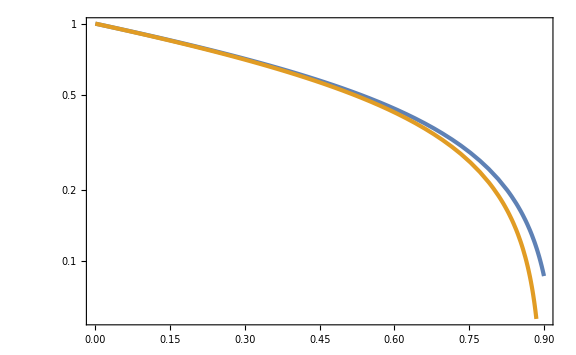

```mathematica
LogPlot[{1/(1+zsol[t0sol-dt]),aanal[t0anal-dt]},{dt,0,t0anal}]
```

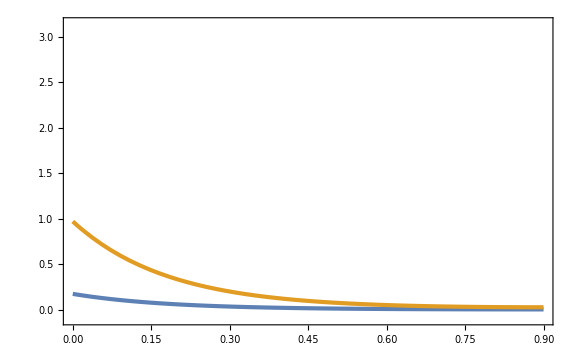

```mathematica
Plot[{xsol[t0sol-dt]/fs,xanal[t0anal-dt]/fs},{dt,0,t0anal},PlotRange->{-0.1,π}]
```

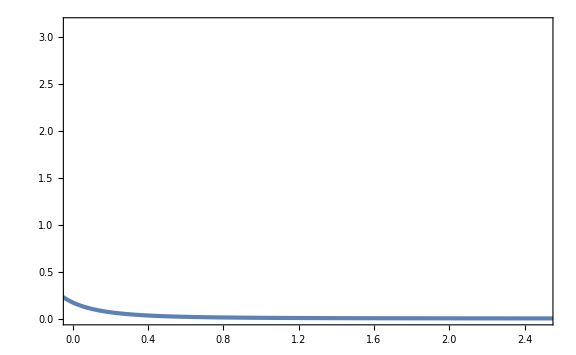

```mathematica
ParametricPlot[{zsol[t],xsol[t]/fs},{t,0,tf},PlotRange->{{0,2.5},{0,π}}]
```

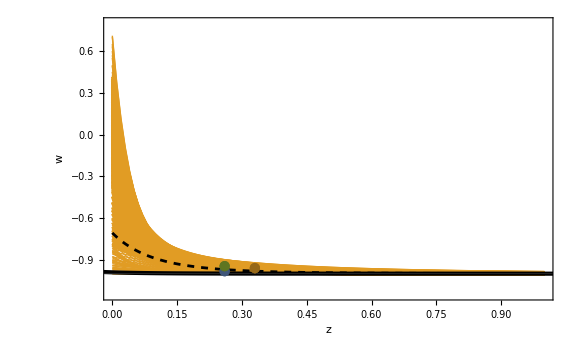

```mathematica
Show[ListPlot[w2sList,PlotRange->{{0,1},{-1.15,0.8}},PlotStyle->{{Thin,Color[2]}},GridLines->{None,{-1}},FrameLabel->{z,w}],ListPlot[w1sList,PlotStyle->{{AbsoluteThickness[2],Color[2]}},PlotRange->Full],ParametricPlot[{zsol[t],wsol[t]},{t,0,tf},PlotStyle->{AbsoluteThickness[3],Black}],Plot[w[1/(1+z)]/.{w0->ws,KK->Ks,Ωϕ->1-Ωms},{z,0,1},PlotRange->Full,PlotStyle->{Black,AbsoluteThickness[2],Dashed}],
ListPlot[{{{0.26,-0.982±0.028}},{{0.33,-0.96±0.038}},{{0.26,-0.946±0.026}}},Joined->False,PlotStyle->{Darker[Color[1]],Darker[Color[2]],Darker[Color[3]]}]]
```

## Axion

```mathematica
V[x_]=Λ2 f^2(1+Cos[x/f]);
```

```mathematica
ws=-1/2;
Ks=5;
Ωms=325/1000;
```

```mathematica
G[a_]=(K Sqrt[(a^3 Ωϕ)/(1-Ωϕ)]Cosh[K ArcSinh[Sqrt[(a^3 Ωϕ)/(1-Ωϕ)]]]-Sqrt[1+(a^3 Ωϕ)/(1-Ωϕ)]Sinh[K ArcSinh[Sqrt[(a^3 Ωϕ)/(1-Ωϕ)]]])/((a^3 Ωϕ)/(1-Ωϕ));
Vnorm[a_]=1-1/2(1+w0)(K^2(1-K^2))/G[1]^2(1-((1-Ωϕ)Sinh[K ArcSinh[Sqrt[(a^3 Ωϕ)/(1-Ωϕ)]]]^2)/(a^3 K^2 Ωϕ));
Kin[a_]=(1+w0)/2 G[a]^2/G[1]^2;
ρnorm[a_]=Vnorm[a]+Kin[a];
```

```mathematica
(Kin[1]-Vnorm[1])/(Kin[1]+Vnorm[1])/.{w0->ws,K->Ks,Ωϕ->1-Ωms}//N
```

-0.398687

```mathematica
Vnorm[1]//Simplify
```

1+((-1+K^2) (1+w0) Ωϕ (K^2 Ωϕ+(-1+Ωϕ) Sinh[K ArcSinh[√(-Ωϕ/(-1+Ωϕ))]]^2))/(2 (-1+Ωϕ)^2 (K √(-Ωϕ/(-1+Ωϕ)) Cosh[K ArcSinh[√(-Ωϕ/(-1+Ωϕ))]]-√(1/(1-Ωϕ)) Sinh[K ArcSinh[√(-Ωϕ/(-1+Ωϕ))]])^2)

```mathematica
-Sqrt[3/4(1+w0)(K^2(1-K^2)^2)/G[1]^2]/.{w0->ws,K->Ks,Ωϕ->1-Ωms}//N
3/4(1-K^2)/.{w0->ws,K->Ks,Ωϕ->1-Ωms}//N
```

-0.168103

-18.

```mathematica
fs=f/.Solve[{V'[xc]/V[xc]==-Sqrt[3/4(1+w0)(K^2(1-K^2)^2)/G[1]^2],V''[xc]/V[xc]==3/4(1-K^2)}/.{w0->ws,K->Ks,Ωϕ->1-Ωms},{f,xc}][[2]];fs//N
xcs=xc/.Solve[{V'[xc]/V[xc]==-Sqrt[3/4(1+w0)(K^2(1-K^2)^2)/G[1]^2],V''[xc]/V[xc]==3/4(1-K^2)}/.{w0->ws,K->Ks,Ωϕ->1-Ωms},{f,xc}][[2]];N[xcs/fs,30]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

0.166601

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

0.0559977081469629402081975359747

```mathematica
xcs/fs//N
```

0.0559977

```mathematica
Λ2s=Λ2/.Solve[V[xc]/3==Ωϕ/ρnorm[1]/.{w0->ws,K->Ks,Ωϕ->1-Ωms,f->fs,xc->xcs},Λ2][[1]];Λ2s//N
```

43.9045

```mathematica
Hnorm[z_,x_,p_]=Sqrt[Ωm(1+z)^3+(p^2/2+V[x])/3]/.{Ωm->Ωms};
```

```mathematica
tf=2;
sol=NDSolve[{x''[t]+3Hnorm[z[t],x[t],x'[t]]x'[t]+V'[x[t]]==0/.{f->fs,Λ2->Λ2s},
x[0]==xcs,x'[0]==0,
z'[t]==-Hnorm[z[t],x[t],x'[t]](1+z[t])/.{f->fs,Λ2->Λ2s},z[0]==1000},{z[t],x[t],x'[t]},{t,0,tf},WorkingPrecision->30,MaxSteps->10^5][[1]]
```

{z[t]→InterpolatingFunction[…][t],x[t]→InterpolatingFunction[{{0, 2.00000000000000000000000000000}}, <>][t],x'[t]→InterpolatingFunction[{{0, 2.00000000000000000000000000000}}, <>][t]}

```mathematica
zsol[t_]=z[t]/.sol;
xsol[t_]=x[t]/.sol;
psol[t_]=x'[t]/.sol;
wsol[t_]=(psol[t]^2/2-V[xsol[t]])/(psol[t]^2/2+V[xsol[t]])/.{f->fs,Λ2->Λ2s};
ρsol[t_]=psol[t]^2/2+V[xsol[t]]/.{f->fs,Λ2->Λ2s};
Hsol[t_]=Hnorm[zsol[t],xsol[t],psol[t]]/.{f->fs,Λ2->Λ2s};
```

```mathematica
F[a_]=Sqrt[1+(Ωϕ^-1-1)a^-3];
calF[a_]=(((K-F[a])(F[a]+1)^K+(K+F[a])(F[a]-1)^K)/((K-Ωϕ^(-1/2))(Ωϕ^(-1/2)+1)^K+(K+Ωϕ^(-1/2))(Ωϕ^(-1/2)-1)^K))^2;
w[a_]=-1+(1+w0)a^(3(K-1))calF[a];
```

```mathematica
aanal[t_]=((1-Ωϕ)/Ωϕ)^(1/3)Sinh[t/tΛ]^(2/3)/.{tΛ->2/Sqrt[3V[xcs]]}/.{f->fs,Λ2->Λ2s,Ωϕ->1-Ωms};
xanal[t_]=xcs+V'[xcs]/V''[xcs](Sinh[k t]/(k tΛ Sinh[t/tΛ])-1)/.{tΛ->2/Sqrt[3V[xcs]],k->Sqrt[3/4 V[xcs]-V''[xcs]]}/.{f->fs,Λ2->Λ2s,Ωϕ->1-Ωms};
tanal[a_]=InverseFunction[aanal][a];
Hanal[a_]=Sqrt[(1-Ωϕ)a^-3+Ωϕ ρnorm[a]/ρnorm[1]]/.{w0->ws,K->Ks,Ωϕ->1-Ωms};
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

```mathematica
t0sol=t/.FindRoot[zsol[t]==0,{t,tf/2}]
t0anal=t/.FindRoot[aanal[t]==1,{t,tf/2}]
```

0.934292

0.911242

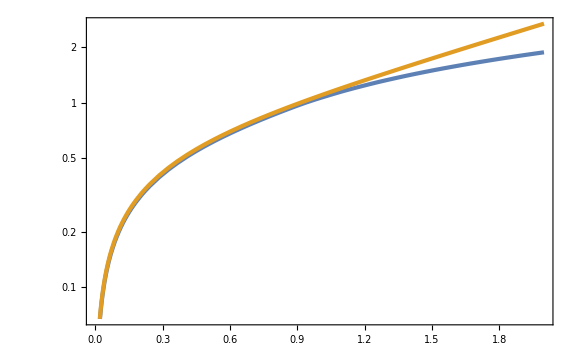

```mathematica
LogPlot[{1/(1+zsol[t]),aanal[t]},{t,0,tf}]
```

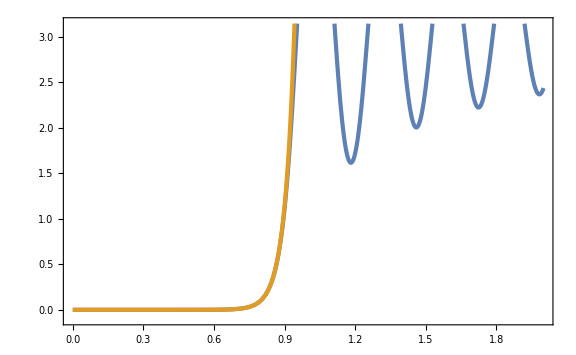

```mathematica
Plot[{xsol[t]/fs,xanal[t]/fs},{t,0,tf},PlotRange->{-0.1,π}]
```

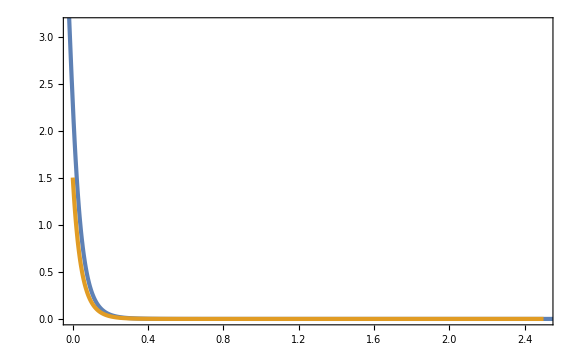

```mathematica
Show[ParametricPlot[{zsol[t],xsol[t]/fs},{t,0,tf},PlotRange->{{0,2.5},{0,π}}],Plot[xanal[tanal[1/(1+z)]]/fs,{z,0,2.5},PlotRange->Full,PlotStyle->{Color[2],AbsoluteThickness[3]}]]
```

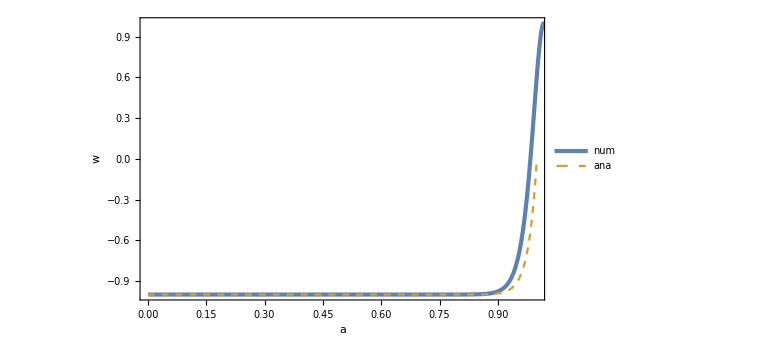

```mathematica
Show[ParametricPlot[{{1/(1+zsol[t]),wsol[t]},{1,1}},{t,0,tf},PlotRange->{{0,1},Full},FrameLabel->{{w,None},{a,Row[{Subscript[w, 0]==0,",  ",K==20}]}},PlotLegends->Placed[{"num","ana"},{0.3,0.7}],PlotStyle->{AbsoluteThickness[3],Dashed}],Plot[w[a]/.{w0->ws,K->Ks,Ωϕ->1-Ωms},{a,0,1},PlotRange->Full,PlotStyle->{Color[2],Dashed}]]
```

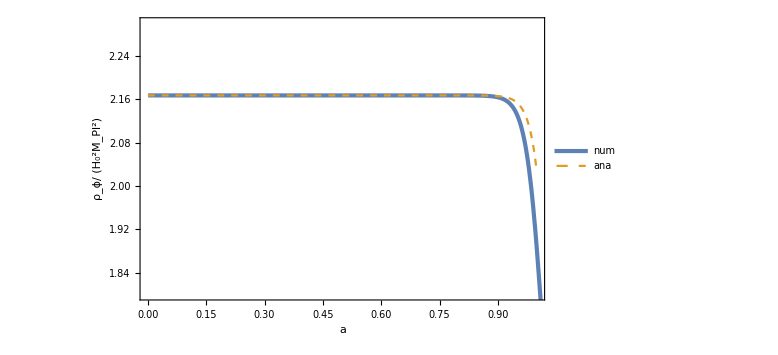

```mathematica
Show[ParametricPlot[{{1/(1+zsol[t]),ρsol[t]},{1,1}},{t,0,tf},PlotRange->{{0,1},{1.8,2.3}},FrameLabel->{{Row[{Subscript[ρ, ϕ],"/ (H_0^2M_Pl^2)"}],None},{a,Row[{Subscript[w, 0]==0,",  ",K==20}]}},PlotLegends->Placed[{"num","ana"},{0.3,0.2}],PlotStyle->{AbsoluteThickness[3],Dashed}],Plot[3Ωϕ ρnorm[a]/ρnorm[1]/.{w0->ws,K->Ks,Ωϕ->1-Ωms},{a,0,1},PlotRange->Full,PlotStyle->{Color[2],Dashed}]]
```

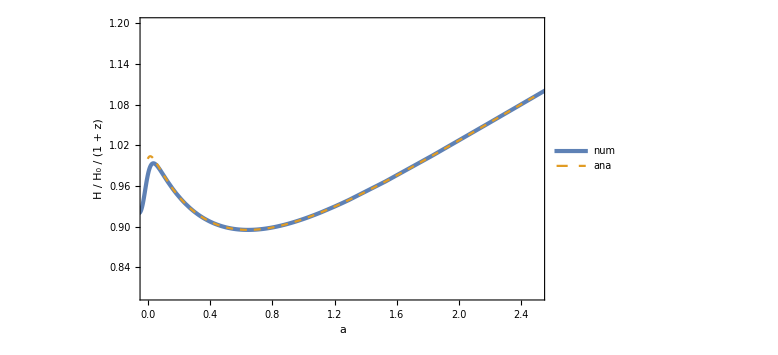

```mathematica
Show[ParametricPlot[{{zsol[t],Hsol[t]/(1+zsol[t])},{1,10}},{t,0,tf},PlotRange->{{0,2.5},{0.8,1.2}},FrameLabel->{{Row[{H," / ",Subscript[H, 0]," / (1 + z)"}],None},{a,Row[{Subscript[w, 0]==0,",  ",K==20}]}},PlotLegends->Placed[{"num","ana"},{0.3,0.7}],PlotStyle->{AbsoluteThickness[3],Dashed}],Plot[Hanal[1/(1+z)]/(1+z),{z,0,2.5},PlotStyle->{Color[2],Dashed}]]
```

```mathematica
Hsol[t0sol]
Ωms/Hsol[t0sol]^2
(ρsol[t0sol]/3)/Hsol[t0sol]^2
```

0.976216

0.341029

0.658971

## Axion MCMC

```mathematica
fs=1/10;
Λ2s=7^2;
xcs=10^-3 fs;
Ωmh2=10^-1;
```

```mathematica
V[x_]=Λ2s fs^2(1+Cos[x/fs]);
```

```mathematica
Hnorm[z_,x_,p_]=Sqrt[Ωmh2(1+z)^3+(p^2/2+V[x])/3];
```

```mathematica
tf=3;
sol=NDSolve[{x''[t]+3Hnorm[z[t],x[t],x'[t]]x'[t]+V'[x[t]]==0,
x[0]==xcs,x'[0]==0,
z'[t]==-Hnorm[z[t],x[t],x'[t]](1+z[t]),z[0]==1000},{z[t],x[t],x'[t]},{t,0,tf},WorkingPrecision->30,MaxSteps->10^5][[1]]
```

{z[t]→InterpolatingFunction[…][t],x[t]→InterpolatingFunction[…][t],x'[t]→InterpolatingFunction[…][t]}

```mathematica
zsol[t_]=z[t]/.sol;
xsol[t_]=x[t]/.sol;
psol[t_]=x'[t]/.sol;
wsol[t_]=(psol[t]^2/2-V[xsol[t]])/(psol[t]^2/2+V[xsol[t]]);
ρsol[t_]=psol[t]^2/2+V[xsol[t]];
Hsol[t_]=Hnorm[zsol[t],xsol[t],psol[t]];
t0sol=t/.FindRoot[zsol[t]==0,{t,tf/2}]
```

1.58878

```mathematica
Ωϕ=ρsol[t0sol]/(3 Hsol[t0sol]^2)
KK=Sqrt[1-4/3 V''[xcs]/V[xcs]];KK//N
w0=wsol[t0sol]
```

0.71188

8.22597

0.406998

```mathematica
1-Ωmh2/Hsol[t0sol]^2
```

0.71188

```mathematica
F[a_]=Sqrt[1+(Ωϕ^-1-1)a^-3];
calF[a_]=(((KK-F[a])(F[a]+1)^KK+(KK+F[a])(F[a]-1)^KK)/((KK-Ωϕ^(-1/2))(Ωϕ^(-1/2)+1)^KK+(KK+Ωϕ^(-1/2))(Ωϕ^(-1/2)-1)^KK))^2;
w[a_]=-1+(1+w0)a^(3(KK-1))calF[a];
```

```mathematica
G[a_]=(KK Sqrt[(a^3 Ωϕ)/(1-Ωϕ)]Cosh[KK ArcSinh[Sqrt[(a^3 Ωϕ)/(1-Ωϕ)]]]-Sqrt[1+(a^3 Ωϕ)/(1-Ωϕ)]Sinh[KK ArcSinh[Sqrt[(a^3 Ωϕ)/(1-Ωϕ)]]])/((a^3 Ωϕ)/(1-Ωϕ));
Vnorm[a_]=1-1/2(1+w0)(KK^2(1-KK^2))/G[1]^2(1-((1-Ωϕ)Sinh[KK ArcSinh[Sqrt[(a^3 Ωϕ)/(1-Ωϕ)]]]^2)/(a^3 KK^2 Ωϕ));
Kin[a_]=(1+w0)/2 G[a]^2/G[1]^2;
ρnorm[a_]=Vnorm[a]+Kin[a];
```

```mathematica
Hanal[a_]=Sqrt[(1-Ωϕ)a^-3+Ωϕ ρnorm[a]/ρnorm[1]];
```

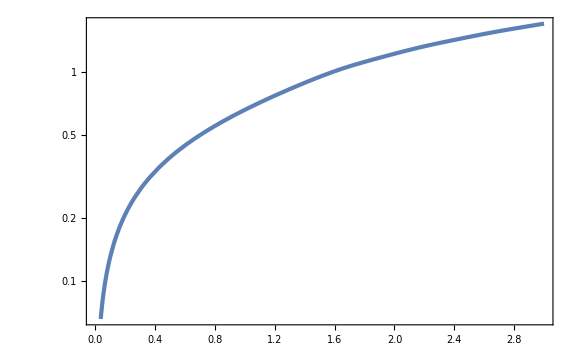

```mathematica
LogPlot[1/(1+zsol[t]),{t,0,tf}]
```

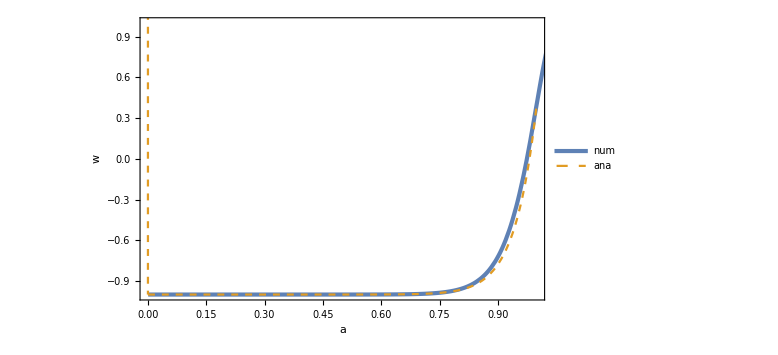

```mathematica
Show[ParametricPlot[{{1/(1+zsol[t]),wsol[t]},{1,1}},{t,0,tf},PlotRange->{{0,1},Full},FrameLabel->{a,w},PlotLegends->Placed[{"num","ana"},{0.3,0.7}],PlotStyle->{AbsoluteThickness[3],Dashed}],
Plot[w[a],{a,0,1},PlotRange->Full,PlotStyle->{Color[2],Dashed}]]
```

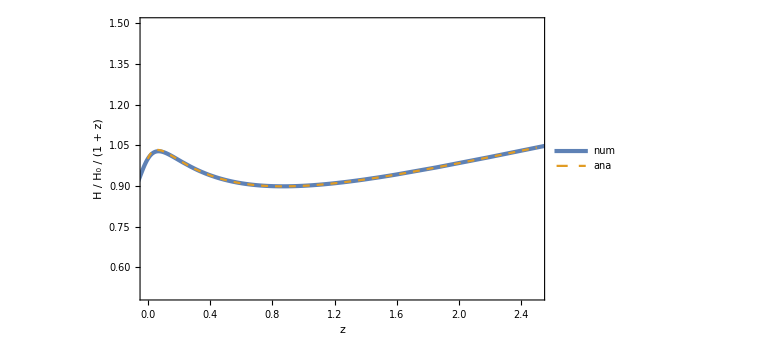

```mathematica
Show[ParametricPlot[{{zsol[t],(Hsol[t]/Hsol[t0sol])/(1+zsol[t])},{1,10}},{t,0,tf},PlotRange->{{0,2.5},{0.5,1.5}},FrameLabel->{z,Row[{H," / ",Subscript[H, 0]," / (1 + z)"}]},PlotLegends->Placed[{"num","ana"},{0.3,0.7}],PlotStyle->{AbsoluteThickness[3],Dashed}],Plot[Hanal[1/(1+z)]/(1+z),{z,0,2.5},PlotRange->Full,PlotStyle->{Color[2],Dashed}]]
```

## Tanh

```mathematica
fs=10^-3;
xcs=735/100 fs;
Ωm=0.3;
Λs4=3(1-Ωm) 100/90;
```

```mathematica
V[x_]=Λs4 Tanh[x/fs]^2;
Hnorm[z_,x_,p_]=Sqrt[Ωm(1+z)^3+(p^2/2+V[x])/3];
tf=3;
sol=NDSolve[{x''[t]+3Hnorm[z[t],x[t],x'[t]]x'[t]+V'[x[t]]==0,
x[0]==xcs,x'[0]==0,
z'[t]==-Hnorm[z[t],x[t],x'[t]](1+z[t]),z[0]==1000},{z[t],x[t],x'[t]},{t,0,tf}(*,WorkingPrecision->30,MaxSteps->10^5*)][[1]];
zsol[t_]=z[t]/.sol;
xsol[t_]=x[t]/.sol;
psol[t_]=x'[t]/.sol;
wsol[t_]=(psol[t]^2/2-V[xsol[t]])/(psol[t]^2/2+V[xsol[t]]);
ρsol[t_]=psol[t]^2/2+V[xsol[t]];
Hsol[t_]=Hnorm[zsol[t],xsol[t],psol[t]];
t0sol=t/.FindRoot[zsol[t]==0,{t,tf/2}]
Ωϕsol[t_]=ρsol[t]/(3 Hsol[t]^2);
Ωmsol[t_]=1-Ωϕsol[t];
Ωϕsol[t0sol]
Hsol[t0sol]
```

0.949745

0.700126

1.00021

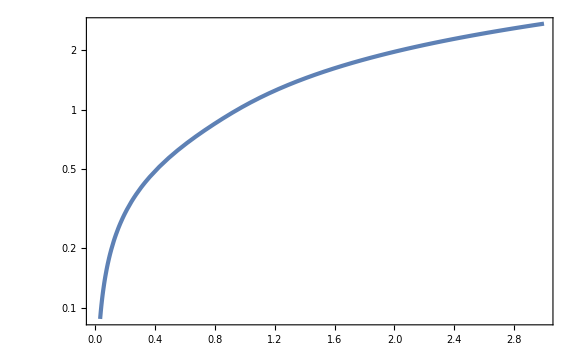

```mathematica
LogPlot[1/(1+zsol[t]),{t,0,tf}]
```

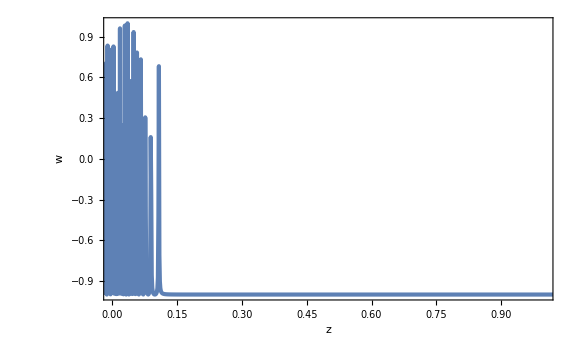

```mathematica
ParametricPlot[{zsol[t],wsol[t]},{t,0,tf},PlotRange->{{0,1},Full},FrameLabel->{z,w}]
```

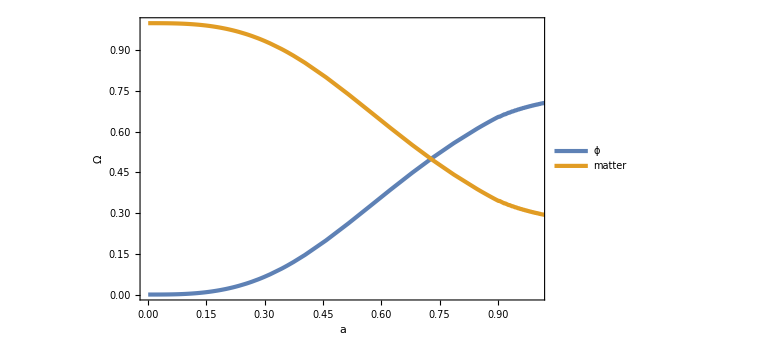

```mathematica
ParametricPlot[{{1/(1+zsol[t]),Ωϕsol[t]},{1/(1+zsol[t]),Ωmsol[t]}},{t,0,tf},PlotRange->{{0,1},Full},FrameLabel->{a,Ω},PlotLegends->Placed[{ϕ,matter},{0.8,0.2}]]
```

```mathematica
zc=0.1;
wc=-0.7;
HnormStep[z_]:=Sqrt[Ωm(1+z)^3+(1-Ωm)(1+z)^(3(1+wc))]/;z<=zc
HnormStep[z_]:=Sqrt[Ωm(1+z)^3+(1-Ωm)(1+zc)^(3(1+wc))]/;z>zc
```

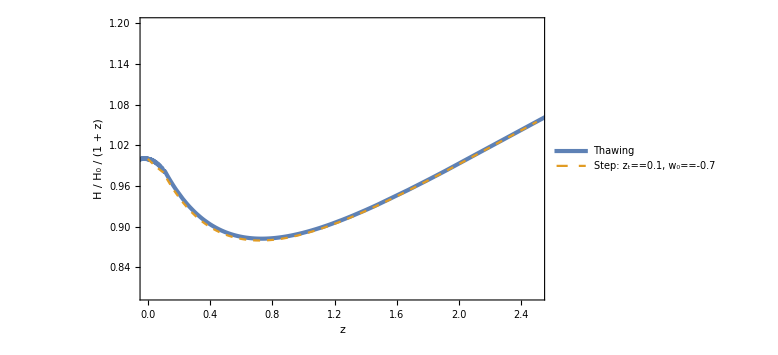

```mathematica
Show[ParametricPlot[{{zsol[t],(Hsol[t]/Hsol[t0sol])/(1+zsol[t])},{-1,-1}},{t,0,tf},PlotRange->{{0,2.5},{0.8,1.2}},FrameLabel->{z,Row[{H," / ",Subscript[H, 0]," / (1 + z)"}]},PlotLegends->Placed[{Thawing,Row[{"Step: ",Subscript[z, "t"]==0.1,", ",Subscript[w, 0]==-0.7}]},{0.4,0.8}],PlotStyle->{AbsoluteThickness[3],Dashed}],
Plot[HnormStep[z]/(1+z),{z,0,2.5},PlotStyle->{Color[2],Dashed}]]
```